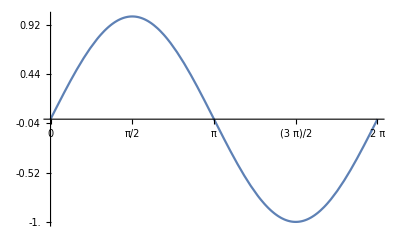

```mathematica
Plot[Sin[x],{x,0,2π},Ticks->{Range[0,2π,π/4],Range[-1,1,0.24]}]
```

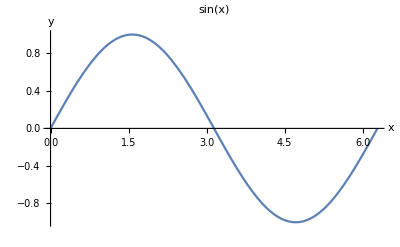

```mathematica
Plot[Sin[x],{x,0,2π},PlotLabel->"sin(x)",
AxesLabel->{"x","y"}]
```

```mathematica
Plot[Sin[x],{x,0,2π},
PlotLabel->Style["sin(x)",FontSize->14,FontFamily->"Arial",
FontColor->Blue],
AxesLabel->{Style["x",FontSize->14,Bold],Style["y",FontSize->14,
Bold]}]
```

-Graphics-

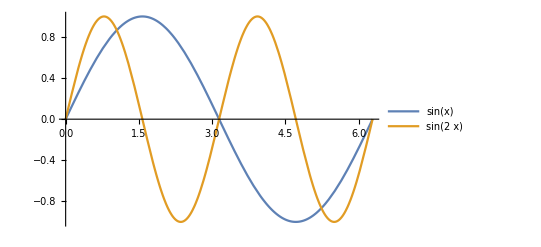

```mathematica
Plot[{Sin[x],Sin[2 x]},{x,0,2 π},PlotLegends->"Expressions"]
```

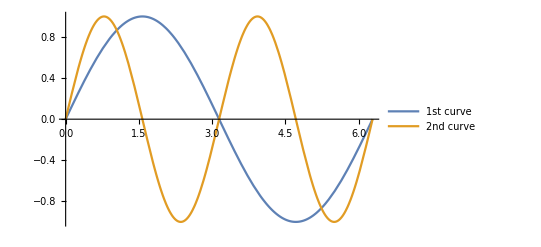

```mathematica
Plot[{Sin[x],Sin[2x]},{x,0,2π},
PlotLegends->{"1st curve", "2nd curve"}]
```

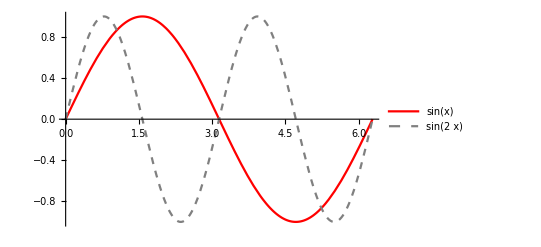

```mathematica
Plot[{Sin[x],Sin[2x]},{x,0,2π},
PlotStyle->{{Red, Thick},{Gray,Thick,Dashed}},
PlotLegends->"Expressions"]
```

```mathematica
Plot[{Sin[x],Sin[2x]},{x,0,2π},
PlotStyle->{{Red,Thick},{Gray,Thick,Dashed}},
PlotLegends->Placed["Expressions",Left]]
```

-Graphics-

```mathematica
Plot[{Callout[Sin[x],"sin(x)"],
Callout[Cos[x],"cos(x)"]},
{x,0,2π}, PlotStyle->{{Red,Thick},{Gray,Thick,Dashed}}]
```

-Graphics-

```mathematica
Plot[{Callout[Sin[x],"sin(x)", Top],
Callout[Cos[x],"cos(x)", Bottom]},
{x,0,2π}, PlotStyle->{{Red,Thick},{Gray,Thick,Dashed}}]
```

-Graphics-

```mathematica
Plot[Callout[Tan[x],"tan(x)",2.5],{x,0,2π}]
```

-Graphics-

```mathematica
Plot[Callout[Tan[x],"tan(x)",2.5],{x,0,2π},Epilog->Point[{π,0}]]
```

-Graphics-

```mathematica
Plot[Callout[Tan[x],"tan(x)",2.5],{x,0,2π},Epilog->{PointSize[Large],Point[{π,0}]}]
```

-Graphics-

```mathematica
Plot3D[Sin[x y],{x,0,π},{y, 0,π},Mesh->None]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[u],Sin[u]+Cos[v],Sin[v]},{u,0,2π},{v,-π,π},
PlotStyle->Opacity[.4],Mesh->None]
```

-Graphics3D-

```mathematica
SphericalPlot3D[1+Sin[5ϕ] Sin[10θ]/10,{θ,0,π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[1+Sin[5ϕ] Sin[10θ]/10,{θ,0,π},{ϕ,0,2π},
Axes->False,
Mesh->True,
Boxed->False,
Background->Black,
Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
SphericalPlot3D[1+Sin[5ϕ] Sin[10θ]/10,{θ,0,π},{ϕ,0,2π},
Axes->False,
Mesh->False,
Boxed->False,
Background->Black,
Lighting->"Neutral",
PlotStyle->{Texture[ExampleData[{"Texture","Water3"}]]}]
```

-Graphics3D-

```mathematica
ExampleData["Texture"]
```

{{Texture,Bark},{Texture,Bark2},{Texture,Bark3},{Texture,Bricks},{Texture,Bricks2},{Texture,Bricks3},{Texture,Bricks4},{Texture,Bricks5},{Texture,Bricks6},{Texture,Bricks7},{Texture,Bricks8},{Texture,BrickWall},{Texture,Bubbles},{Texture,Bubbles2},{Texture,Bubbles3},{Texture,Cloth},{Texture,Cloth2},{Texture,Cloth3},{Texture,Grass},{Texture,Grass2},{Texture,Grass3},{Texture,Grass4},{Texture,Grass5},{Texture,Gravel},{Texture,Herringbone},{Texture,Herringbone2},{Texture,Herringbone3},{Texture,HexagonalHoles},{Texture,Leather},{Texture,Leather2},{Texture,Leather3},{Texture,MetalGrates},{Texture,Mosaic},{Texture,Mosaic2},{Texture,Mosaic3},{Texture,Mosaic4},{Texture,Mosaic5},{Texture,Mosaic6},{Texture,Pigskin},{Texture,Pigskin2},{Texture,Pigskin3},{Texture,Raffia},{Texture,Raffia2},{Texture,Raffia3},{Texture,Sand},{Texture,Sand2},{Texture,Sand3},{Texture,Sand4},{Texture,Sand5},{Texture,Sand6},{Texture,Shingles},{Texture,Shingles2},{Texture,Straw},{Texture,Straw2},{Texture,Straw3},{Texture,TileRoof},{Texture,Wall},{Texture,Water},{Texture,Water2},{Texture,Water3},{Texture,Wood},{Texture,Wood2},{Texture,Wood3},{Texture,WoodFence}}

```mathematica
ExampleData[{"Texture","Water2"}]
```

-Graphics-

```mathematica
myPlot[eq1_,eq2_]:=
Plot[{eq1,eq2},{x,0,2π},
PlotStyle->{{Red,Thick},{Gray,Thick,Dashed}},
PlotLegends->Placed["Expressions",Above]]
```

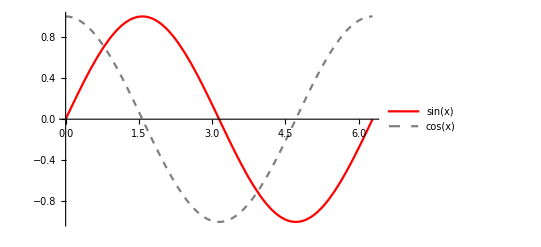

```mathematica
myPlot[Sin[x],Cos[x]]
```

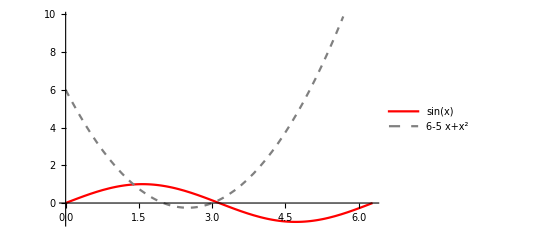

```mathematica
myPlot[Sin[x],x^2-5x+6]
```

```mathematica
mySettings=PlotStyle->{{Red,Thick},{Gray,Thick,Dashed}};
```

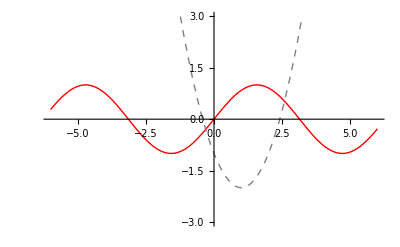

```mathematica
Plot[{Sin[x],x^2-2x-1},{x,-6,6},PlotRange->3,
Evaluate[mySettings]]
```

```mathematica
Clear[myPlot,mySettings]
```

## Exercises

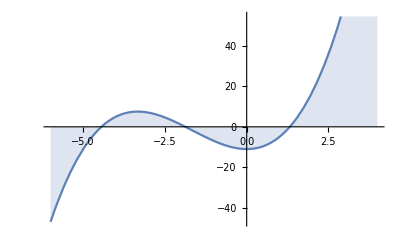

```mathematica
Plot[x^3+5 x^2-11,{x,-6,4},Filling->Axis]
```

WolframAlphaQueryParseResults

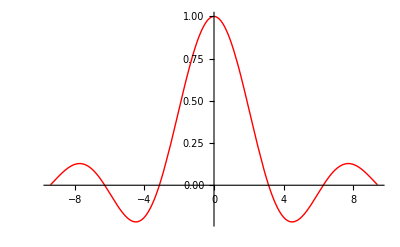

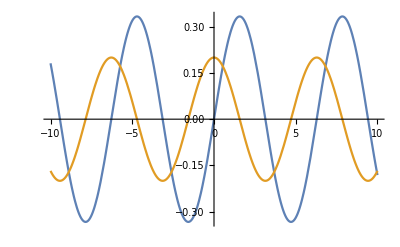

```mathematica
Plot[{Sin[x]/3,Cos[x]/5},{x,-10,10}]
```

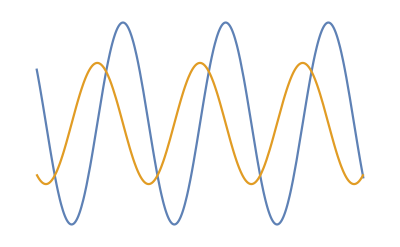

```mathematica
Show[Plot[{Sin[x]/3,Cos[x]/5},{x,-10,10}],Background->None,Axes->False]
```

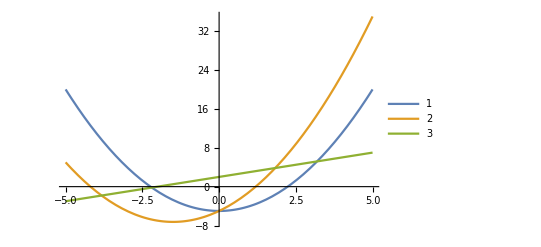

```mathematica
Plot[{x^2-5,x^2+3x-5,x+2},{x,-5,5},
PlotLegends->{"1","2","3"}]
```

```mathematica
Plot3D[Table[x^2-y,100],{x,-π,π},{y,-π,π},Boxed->False,Mesh->False,Axes->False]
```

-Graphics3D-

```mathematica
Table[x^2-y,100]
```

{x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y,x^2-y}

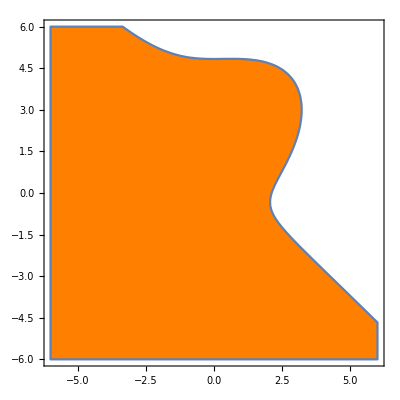

```mathematica
RegionPlot[x^3 - x^2 + y^3 - 4*y^2 - 3*y < 5, {x, -6., 6.}, {y, -6., 6.}, PlotStyle->Orange]
```

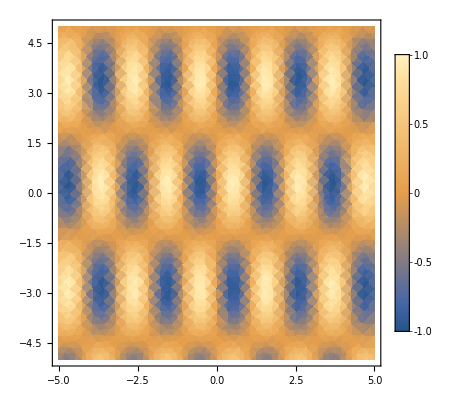

```mathematica
DensityPlot[Sin[3x]Sin[y-5],{x,-5,5},{y,-5,5},PlotLegends->Automatic]
```

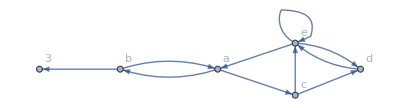

```mathematica
Graph[{a->b,a->c,b->a,b->3,c->d,c->e,d->e,e->a,e->d,e->e},
VertexLabels->Automatic, DirectedEdges->True]
```

```mathematica
data = Table[RandomInteger[{0,5},5],10];
```

```mathematica
BarChart3D[data,ChartLayout->"Stacked"]
```

-Graphics3D-